```mathematica
SetDirectory[NotebookDirectory[]]
```

## A MANUAL FOR SECTION 3: OBSERVATIONAL PREDICTIONS AND RESULTS

```mathematica
(*We use Equation (23) in order to define the function Subscript[δ, max]≡dta which correspond to the overdensity at the moment of turnaround*)

dta[om0m_?NumericQ,om0l_?NumericQ,a_?NumericQ]:=Module[{omi,xi,fn1,root},
(*Calculate omi which corresponds to ω (see Equation (11)) and xi≡ξ (see Equation (12)) based on om0m≡Subscript[Ω, m,0] and om0l≡Subscript[Ω, Λ,0]*)omi=om0l/om0m;
xi=(1-om0l-om0m)/om0m;
(*Define the function fn1*)fn1[dta_?NumericQ]:=Module[{integrand1,integrand2,integral1,integral2},
(*Provide a definition for the integrand associated with Equation (23).Specifically,the integrand referenced here,termed as'Integrand1',pertains to the left-hand side of Equation (23), while the right-hand side of Equation (23) correspond to the 'Integrand2' here *)
integrand1=Sqrt[u]/Sqrt[(1-u) ((1+dta)/(omi a^3)-u (u+1))];
(*The selection of the second integrand is contingent upon the value of om0l≡Subscript[Ω, Λ,0]. A positive cosmological constant corresponds to Subscript[Ω, Λ,0]>0 ,while a negative cosmological constant corresponds to Subscript[Ω, Λ,0]<0. *)
If[om0l>0,integrand2=Sqrt[omi] Sqrt[y]/Sqrt[omi y^3+xi y/a^2+1/a^3],integrand2=Sqrt[y]/Sqrt[y^3+xi y/(omi a^2)+1/(omi a^3)]];
(*Perform the numerical integration as indicated in Equation (23)*)
integral1=NIntegrate[integrand1,{u,0,1}];
integral2=NIntegrate[integrand2,{y,0,1}];(*Return the difference between the two integrals*)integral1-integral2];
(*Find the root of the function*)root=Quiet[FindRoot[fn1[dta]==0,{dta,14.5,1}]];
(*Return the real part of the root*)Re[dta/. root]]
```

```mathematica
(*The parameter rtarst≡Subscript[R, p,max]/Subscript[R, c] correspond to ratio as indicated in Equation (49)*)
```

```mathematica
rtarst[om0m_?NumericQ,om0l_?NumericQ,a_?NumericQ,mmst_?NumericQ]:=((1+dta[om0m,om0l,a])om0m)^(-1/3)a(mmst)^(1/3);
(*The parameter qq≡ε (See Equation (51)) indicates the ratio of the energy density associated
with the cosmological constant to the energy overdensity*)
```

```mathematica
qq[om0m_?NumericQ,om0l_?NumericQ,a_?NumericQ,mmst_?NumericQ]:=(om0l/om0m) a^3/(dta[om0m,om0l,a]+1)
```

```mathematica
(*The parameter rvirrst≡Subscript[R, vir]/Subscript[R, c], see Equation (52)*)
```

```mathematica
rvirrst[om0m_?NumericQ,om0l_?NumericQ,a_?NumericQ,mmst_?NumericQ]:=rtarst[om0m,om0l,a,mmst](0.5-0.25 qq[om0m,om0l,a,mmst])
```

### Figure 1. The provided diagram offers a comparative representation of the ratio between virialized energy overdensity, given various numerical values for the density parameters Ω_(m,0), Ω_(Λ,0) and curvature Ω_(k,0)≠0 and the virialized energy density within a ΛCDM model where Ω_(m,0) = 0.3 and Ω_(Λ,0) = 0.7. This comparison is illustrated with respect to the turn around redshift, denoted as z_max.

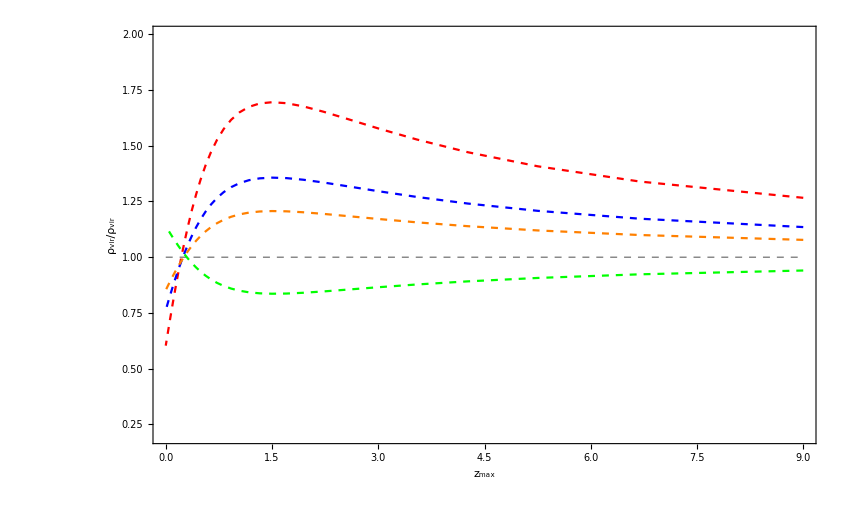

figrhovir1.pdf

```mathematica
tabrvirdens1=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[0.3,-0.7,a,1])^3},{a,0.1,1,0.03}];
pl1a=ListPlot[tabrvirdens1,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Red},{"Ω_(Λ, 0)=-0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Red,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens2=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[0.3,0.00001,a,1])^3},{a,0.1,1,0.03}];
pl2a=ListPlot[tabrvirdens2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Blue},{"Ω_(Λ, 0)=0,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Blue,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[0.3,0.3,a,1])^3},{a,0.1,1,0.03}];
pl3a=ListPlot[tabrvirdens3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Orange,Gray},{"Ω_(Λ, 0)=0.3,Ω_(m, 0)=0.3","Ω_(Λ, 0)=0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Orange,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
pl3b=Graphics[{Gray,Dashed,Line[{{Min[tabrvirdens1[[All,1]]],1},{Max[tabrvirdens1[[All,1]]],1}}]},PlotRange->{0.5,2}];
tabrvirdens4=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[0.3,1.0,a,1])^3},{a,0.1,1,0.03}];
pl4a=ListPlot[tabrvirdens4,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Green},{"Ω_(Λ, 0)=1,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Green,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];

figrhovir1=Show[pl1a,pl2a,pl3a,pl3b,pl4a,PlotRange->{0.2,2},Axes->False,ImageSize->850]
Export["figrhovir1.pdf",figrhovir1]
```

### Figure 2. The provided diagram offers a comparative representation of the ratio between virialized energy overdensity, given various numerical values for the density parameters Ω_(m,0), Ω_(Λ,0) and curvature Ω_k=0 and the virialized energy density within a ΛCDM model where Ω_(m,0) = 0.3 and Ω_(Λ,0)= 0.7. This comparison is illustrated with respect to the turn around redshift, denoted as z_max.

```mathematica
tabrvirdens1=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[1.7,-0.7,a,1])^3},{a,0.1,1,0.03}];
pl1a=ListPlot[tabrvirdens1,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Red},{"Ω_(Λ, 0)=-0.7,Ω_(m, 0)=1.7"}],{0.8,0.2}],PlotStyle->{Red,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens2=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[1,0.00001,a,1])^3},{a,0.1,1,0.03}];
pl2a=ListPlot[tabrvirdens2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Blue},{"Ω_(Λ, 0)=0,Ω_(m, 0)=1"}],{0.8,0.2}],PlotStyle->{Blue,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[0.7,0.3,a,1])^3},{a,0.1,1,0.03}];
pl3a=ListPlot[tabrvirdens3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Orange,Gray},{"Ω_(Λ, 0)=0.3,Ω_(m, 0)=0.7","Ω_(Λ, 0)=0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Orange,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
pl3b=Graphics[{Gray,Dashed,Line[{{Min[tabrvirdens1[[All,1]]],1},{Max[tabrvirdens1[[All,1]]],1}}]},PlotRange->{0.5,2}];
tabrvirdens4=Table[{1/a-1,(rvirrst[0.3,0.7,a,1]/rvirrst[0.02,0.98,a,1])^3},{a,0.1,1,0.03}];
pl4a=ListPlot[tabrvirdens4,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_vir/ρ_vir"},PlotLegends->Placed[LineLegend[{Green},{"Ω_(Λ, 0)=0.98,Ω_(m, 0)=0.02"}],{0.8,0.2}],PlotStyle->{Green,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

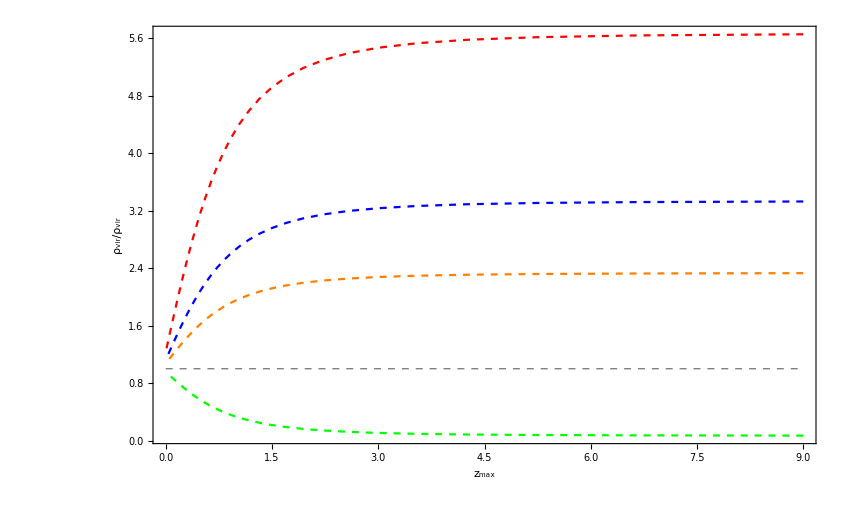

figrhovir2.pdf

```mathematica
figrhovir2=Show[pl1a,pl2a,pl3a,pl3b,pl4a,PlotRange->All,Axes->False,ImageSize->850]
Export["figrhovir2.pdf",figrhovir2]
```

### Figure 3. The turnaround radius, evaluated over a range of density parameters Ω_(m,0) and Ω_(Λ,0), relative to the turnaround radius within a ΛCDM framework constituted by Ω_(m,0) = 0.3 and Ω_(Λ,0) = 0.7, in terms of the turnaround redshift z_max.

```mathematica
tabrvirdens1=Table[{1/a-1,(rtarst[0.3,0.7,a,1]/rtarst[0.3,-0.7,a,1])^-1},{a,0.1,1,0.03}];
pl1a=ListPlot[tabrvirdens1,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/(R_(p, max))"},PlotLegends->Placed[LineLegend[{Red},{"Ω_(Λ, 0)=-0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Red,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens2=Table[{1/a-1,(rtarst[0.3,0.7,a,1]/rtarst[0.3,0.00001,a,1])^-1},{a,0.1,1,0.03}];
pl2a=ListPlot[tabrvirdens2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/(R_(p, max))"},PlotLegends->Placed[LineLegend[{Blue},{"Ω_(Λ, 0)=0,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Blue,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3=Table[{1/a-1,(rtarst[0.3,0.7,a,1]/rtarst[0.3,0.3,a,1])^-1},{a,0.1,1,0.03}];
pl3a=ListPlot[tabrvirdens3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/(R_(p, max))"},PlotLegends->Placed[LineLegend[{Orange,Gray},{"Ω_(Λ, 0)=0.3,Ω_(m, 0)=0.3","Ω_(Λ, 0)=0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Orange,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
pl3b=Graphics[{Gray,Dashed,Line[{{Min[tabrvirdens1[[All,1]]],1},{Max[tabrvirdens1[[All,1]]],1}}]},PlotRange->{0.5,2}];
tabrvirdens4=Table[{1/a-1,(rtarst[0.3,0.7,a,1]/rtarst[0.3,1.0,a,1])^-1},{a,0.1,1,0.03}];
pl4a=ListPlot[tabrvirdens4,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/(R_(p, max))"},PlotLegends->Placed[LineLegend[{Green},{"Ω_(Λ, 0)=1,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Green,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

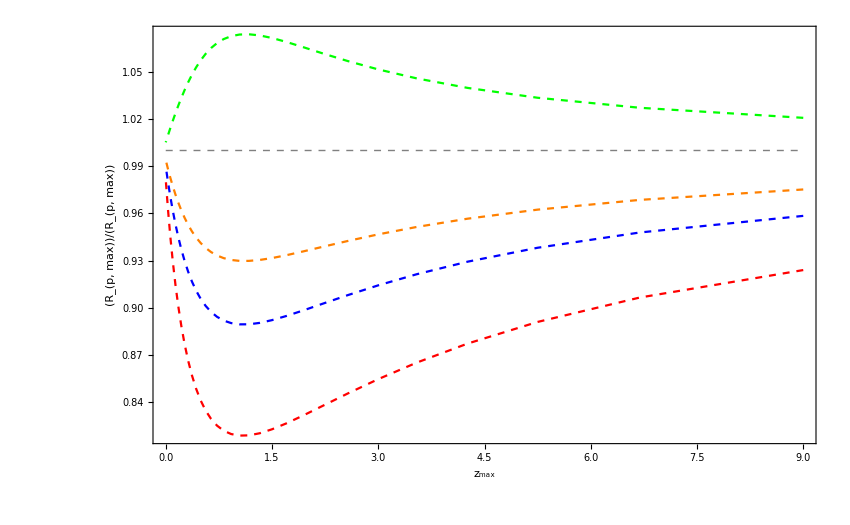

figrta1.pdf

```mathematica
figrta1=Show[pl1a,pl2a,pl3a,pl3b,pl4a,PlotRange->All,Axes->False,ImageSize->850]
Export["figrta1.pdf",figrta1]
```

### Figure 4. The ratio between the turn around radius, considering a range of density parameters Ω_(Λ,0), Ω_(m,0) relative to the length scale R_c, in terms of the turnaround redshift z_max.

```mathematica
tabrvirdens1=Table[{1/a-1,(1/rtarst[0.3,-0.7,a,1])^-1},{a,0.1,1,0.03}];
pl1a=ListPlot[tabrvirdens1,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/R_c"},PlotLegends->Placed[LineLegend[{Red},{"Ω_(Λ, 0)=-0.7,Ω_(m, 0)=0.3"}],{0.8,0.5}],PlotStyle->{Red,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens2=Table[{1/a-1,(1/rtarst[0.3,0.00001,a,1])^-1},{a,0.1,1,0.03}];
pl2a=ListPlot[tabrvirdens2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/R_c"},PlotLegends->Placed[LineLegend[{Blue},{"Ω_(Λ, 0)=0,Ω_(m, 0)=0.3"}],{0.8,0.5}],PlotStyle->{Blue,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3=Table[{1/a-1,(1/rtarst[0.3,0.3,a,1])^-1},{a,0.1,1,0.03}];
pl3a=ListPlot[tabrvirdens3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/R_c"},PlotLegends->Placed[LineLegend[{Orange},{"Ω_(Λ, 0)=0.3,Ω_(m, 0)=0.3"}],{0.8,0.5}],PlotStyle->{Orange,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3b=Table[{1/a-1,(1/rtarst[0.3,0.7,a,1])^-1},{a,0.1,1,0.03}];
pl3b=ListPlot[tabrvirdens3b,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/R_c"},PlotLegends->Placed[LineLegend[{Black},{"Ω_(Λ, 0)=0.7,Ω_(m, 0)=0.3"}],{0.8,0.5}],PlotStyle->{Black,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens4=Table[{1/a-1,(1/rtarst[0.3,1.0,a,1])^-1},{a,0.1,1,0.03}];
pl4a=ListPlot[tabrvirdens4,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","(R_(p, max))/R_c"},PlotLegends->Placed[LineLegend[{Green},{"Ω_(Λ, 0)=1,Ω_(m, 0)=0.3"}],{0.8,0.5}],PlotStyle->{Green,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

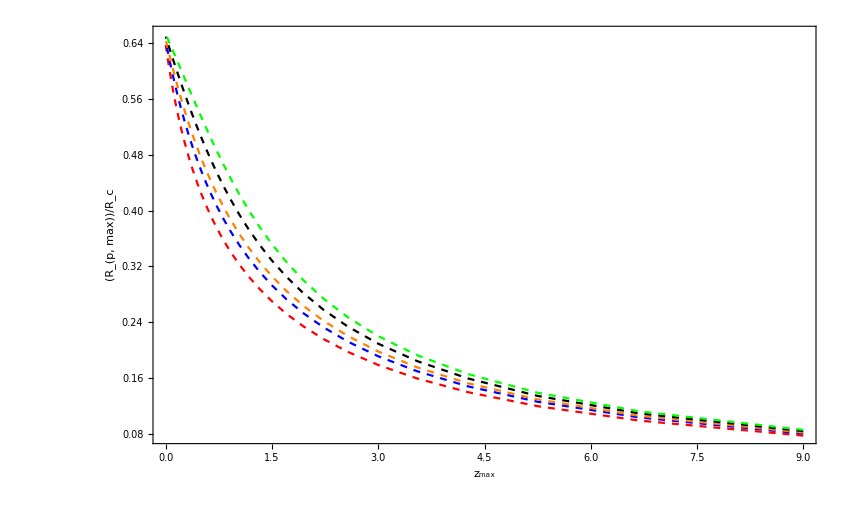

figrta2.pdf

```mathematica
figrta2=Show[pl1a,pl2a,pl3a,pl3b,pl4a,PlotRange->All,Axes->False,ImageSize->850]
Export["figrta2.pdf",figrta2]
```

### Figure 5. The density contrast of 1+ δ_max (Ω_(Λ,0),Ω_(m,0) ) of the Equation (56) i.e energy overdensity at the time of turnaround (t_max) and the corresponding matter energy density of the background at that particular point in time, in terms of the turn around redshift z_max, given various numerical values for the density parameters Ω_(m,0) and Ω_(Λ,0).

```mathematica
tabrvirdens1=Table[{1/a-1,1+dta[0.3,-0.7,a]},{a,0.1,1,0.03}];
pl1a=ListPlot[tabrvirdens1,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","1+δ_max(Ω_(Λ, 0),Ω_(m, 0))"},PlotLegends->Placed[LineLegend[{Red},{"Ω_(Λ, 0)=-0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Red,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens2=Table[{1/a-1,1+dta[0.3,0.00001,a]},{a,0.1,1,0.03}];
pl2a=ListPlot[tabrvirdens2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","1+δ_max(Ω_(Λ, 0),Ω_(m, 0))"},PlotLegends->Placed[LineLegend[{Blue},{"Ω_(Λ, 0)=0,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Blue,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3=Table[{1/a-1,1+dta[0.3,0.3,a]},{a,0.1,1,0.03}];
pl3a=ListPlot[tabrvirdens3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","1+δ_max(Ω_(Λ, 0),Ω_(m, 0))"},PlotLegends->Placed[LineLegend[{Orange},{"Ω_(Λ, 0)=0.3,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Orange,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3b=Table[{1/a-1,1+dta[0.3,0.7,a]},{a,0.1,1,0.03}];
pl3b=ListPlot[tabrvirdens3b,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","1+δ_max(Ω_(Λ, 0),Ω_(m, 0))"},PlotLegends->Placed[LineLegend[{Black},{"Ω_(Λ, 0)=0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Black,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens4=Table[{1/a-1,1+dta[0.3,1,a]},{a,0.1,1,0.03}];
pl4a=ListPlot[tabrvirdens4,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","1+δ_max(Ω_(Λ, 0),Ω_(m, 0))"},PlotLegends->Placed[LineLegend[{Green},{"Ω_(Λ, 0)=1,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Green,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

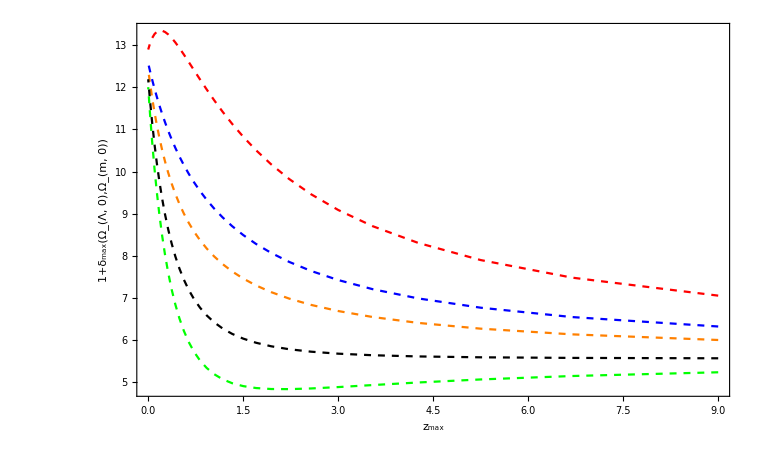

figrhota1.pdf

```mathematica
figrhota1=Show[pl1a,pl2a,pl3a,pl3b,pl4a,PlotRange->All,Axes->False,ImageSize->760]
Export["figrhota1.pdf",figrhota1]
```

### Figure 6. The density contrast parameter ε(z_max;Ω_(Λ,0),Ω_(m,0)) , considering a range of density parameters Ω_(m,0), and Ω_(Λ,0), is demonstrated through the dependency on the turnaround redshift z_max.

```mathematica
tabrvirdens1=Table[{1/a-1,qq[0.3,-0.7,a,1]},{a,0.1,1,0.03}];
pl1a=ListPlot[tabrvirdens1,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_Λ/(ρ_(m, max))"},PlotLegends->Placed[LineLegend[{Red},{"Ω_(Λ, 0)=-0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Red,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens2=Table[{1/a-1,qq[0.3,0.00001,a,1]},{a,0.1,1,0.03}];
pl2a=ListPlot[tabrvirdens2,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_Λ/(ρ_(m, max))"},PlotLegends->Placed[LineLegend[{Blue},{"Ω_(Λ, 0)=0,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Blue,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3=Table[{1/a-1,qq[0.3,0.3,a,1]},{a,0.1,1,0.03}];
pl3a=ListPlot[tabrvirdens3,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_Λ/(ρ_(m, max))"},PlotLegends->Placed[LineLegend[{Orange},{"Ω_(Λ, 0)=0.3,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Orange,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens3b=Table[{1/a-1,qq[0.3,0.7,a,1]},{a,0.1,1,0.03}];
pl3b=ListPlot[tabrvirdens3b,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_Λ/(ρ_(m, max))"},PlotLegends->Placed[LineLegend[{Black},{"Ω_(Λ, 0)=0.7,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Black,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
tabrvirdens4=Table[{1/a-1,qq[0.3,1,a,1]},{a,0.1,1,0.03}];
pl4a=ListPlot[tabrvirdens4,Joined->True,PlotRange->All,Frame->True,FrameLabel->{"z_max","ρ_Λ/(ρ_(m, max))"},PlotLegends->Placed[LineLegend[{Green},{"Ω_(Λ, 0)=1,Ω_(m, 0)=0.3"}],{0.8,0.2}],PlotStyle->{Green,Dashed},BaseStyle->{FontFamily->"Times New Roman",FontSize->14}];
```

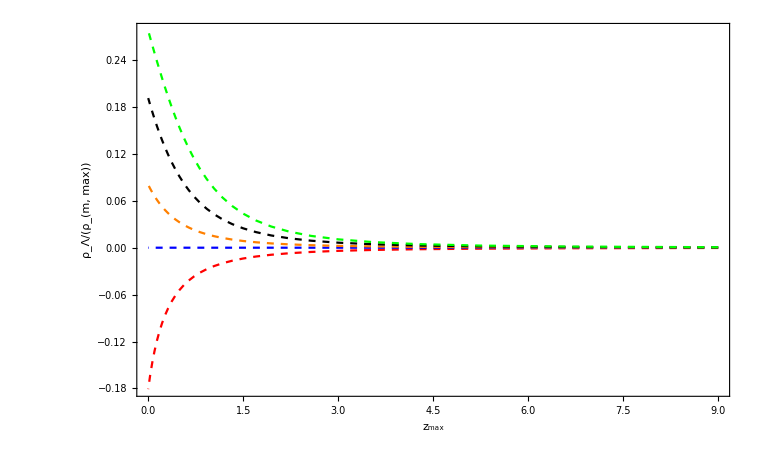

figrholrhom1.pdf

```mathematica
figrholrhom1=Show[pl1a,pl2a,pl3a,pl3b,pl4a,PlotRange->All,Axes->False,ImageSize->760]
Export["figrholrhom1.pdf",figrholrhom1]
```

### Verify that in a cosmological model with Ω_(m,0)=1, has a δ_max(Ω_(m,0)=1,Ω_(Λ,0)=0,a) ,which remains constant across all cosmic epochs, a well-known result in scientific literature.

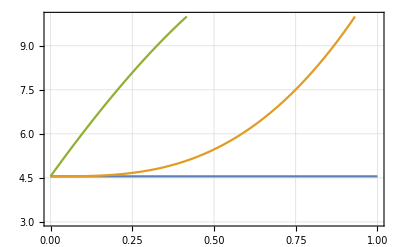

```mathematica
(*For a cosmological model with Subscript[Ω, m,0]=1, the Subscript[δ, max](Subscript[Ω, m,0]=1,Subscript[Ω, Λ,0]=0,a)(Blue line) remains constant across all epochs.In contrast,for a model with Subscript[δ, max](Subscript[Ω, m,0]=0.3,Subscript[Ω, Λ,0]=0.7,a) (Orange line), or a model with Subscript[δ, max](Subscript[Ω, m,0]=0.3,Subscript[Ω, Λ,0]=-0.7,a) (Green line) that is not the case! *)
Plot[{dta[1,0.00001,a],dta[0.3,0.7,a],dta[0.3,-0.7,a]},{a,0,1},PlotRange->{3,10},PlotTheme->"FrameGrid"]
```

## A MANUAL FOR APPENDIX B: VIRIALIZED DARK MATTER WITHIN A HOMOGENEOUS DARK ENERGY-DRIVEN BACKGROUND

### Solving Equation (42) or (B25), where α≡(a_vir/a_max)^(-3(1+w)) , η≡ R_vir/R_max and q≡ε≡ρ_Λ/(ρ_(DM,max)) .

```mathematica
Solve[4 α q η^3 - 2 η (1+q)+1==0,η]
```

{{η→(2 2^(1/3) (1+q))/((-432 q^2 α^2+√(-55296 q^3 (1+q)^3 α^3+186624 q^4 α^4))^(1/3))+((-432 q^2 α^2+√(-55296 q^3 (1+q)^3 α^3+186624 q^4 α^4))^(1/3))/(12 2^(1/3) q α)},{η→-(2^(1/3) (1+ⅈ √3) (1+q))/((-432 q^2 α^2+√(-55296 q^3 (1+q)^3 α^3+186624 q^4 α^4))^(1/3))-((1-ⅈ √3) (-432 q^2 α^2+√(-55296 q^3 (1+q)^3 α^3+186624 q^4 α^4))^(1/3))/(24 2^(1/3) q α)},{η→-(2^(1/3) (1-ⅈ √3) (1+q))/((-432 q^2 α^2+√(-55296 q^3 (1+q)^3 α^3+186624 q^4 α^4))^(1/3))-((1+ⅈ √3) (-432 q^2 α^2+√(-55296 q^3 (1+q)^3 α^3+186624 q^4 α^4))^(1/3))/(24 2^(1/3) q α)}}

### The three solutions η_1, η_2 and η_3 :

```mathematica
eta1[ε_,avir_,amax_,w_]:=(2 2^(1/3) (1-1/2 (1+3 w) ε))/((-108 (avir/amax)^(-6 (1+w)) (1+3 w)^2 ε^2+√(11664 (avir/amax)^(-12 (1+w)) (1+3 w)^4 ε^4+6912 (avir/amax)^(-9 (1+w)) (1+3 w)^3 ε^3 (1-1/2 (1+3 w) ε)^3))^(1/3))-((avir/amax)^(3 (1+w)) (-108 (avir/amax)^(-6 (1+w)) (1+3 w)^2 ε^2+√(11664 (avir/amax)^(-12 (1+w)) (1+3 w)^4 ε^4+6912 (avir/amax)^(-9 (1+w)) (1+3 w)^3 ε^3 (1-1/2 (1+3 w) ε)^3))^(1/3))/(6 2^(1/3) (1+3 w) ε);
eta2[ε_,avir_,amax_,w_]:=-(2^(1/3) (1+ⅈ √3) (1-1/2 (1+3 w) ε))/((-108 (avir/amax)^(-6 (1+w)) (1+3 w)^2 ε^2+√(11664 (avir/amax)^(-12 (1+w)) (1+3 w)^4 ε^4+6912 (avir/amax)^(-9 (1+w)) (1+3 w)^3 ε^3 (1-1/2 (1+3 w) ε)^3))^(1/3))+((1-ⅈ √3) (avir/amax)^(3 (1+w)) (-108 (avir/amax)^(-6 (1+w)) (1+3 w)^2 ε^2+√(11664 (avir/amax)^(-12 (1+w)) (1+3 w)^4 ε^4+6912 (avir/amax)^(-9 (1+w)) (1+3 w)^3 ε^3 (1-1/2 (1+3 w) ε)^3))^(1/3))/(12 2^(1/3) (1+3 w) ε);
eta3[ε_,avir_,amax_,w_]:=-(2^(1/3) (1-ⅈ √3) (1-1/2 (1+3 w) ε))/((-108 (avir/amax)^(-6 (1+w)) (1+3 w)^2 ε^2+√(11664 (avir/amax)^(-12 (1+w)) (1+3 w)^4 ε^4+6912 (avir/amax)^(-9 (1+w)) (1+3 w)^3 ε^3 (1-1/2 (1+3 w) ε)^3))^(1/3))+((1+ⅈ √3) (avir/amax)^(3 (1+w)) (-108 (avir/amax)^(-6 (1+w)) (1+3 w)^2 ε^2+√(11664 (avir/amax)^(-12 (1+w)) (1+3 w)^4 ε^4+6912 (avir/amax)^(-9 (1+w)) (1+3 w)^3 ε^3 (1-1/2 (1+3 w) ε)^3))^(1/3))/(12 2^(1/3) (1+3 w) ε);
```

### The fourth order approximated solution denoted here as η_0 (See Equations (44) and (B32) ) :

```mathematica
eta0[ε_,avir_,amax_,w_]:=1/2+1/8 (-2+(avir/amax)^(-3 (1+w))) (-1-3 w) ε+1/32 (-2+(avir/amax)^(-3 (1+w))) (-2+3 (avir/amax)^(-3 (1+w))) (-1-3 w)^2 ε^2+1/64 (2+6 (avir/amax)^(-6 (1+w))-9 (avir/amax)^(-3 (1+w))) (-2+(avir/amax)^(-3 (1+w))) (-1-3 w)^3 ε^3+1/512 (-2+(avir/amax)^(-3 (1+w))) (-8+(avir/amax)^(-3 (1+w)) (76+5 (avir/amax)^(-3 (1+w)) (-26+11 (avir/amax)^(-3 (1+w))))) (-1-3 w)^4 ε^4;
```

### Figure B2. Three solutions (shades of red) derived from equation (B30), by assuming a value of w=-1. Additionally, a line rendered in light gray within the plot delineates an approximation up to the fourth order, as outlined in equation (B33).

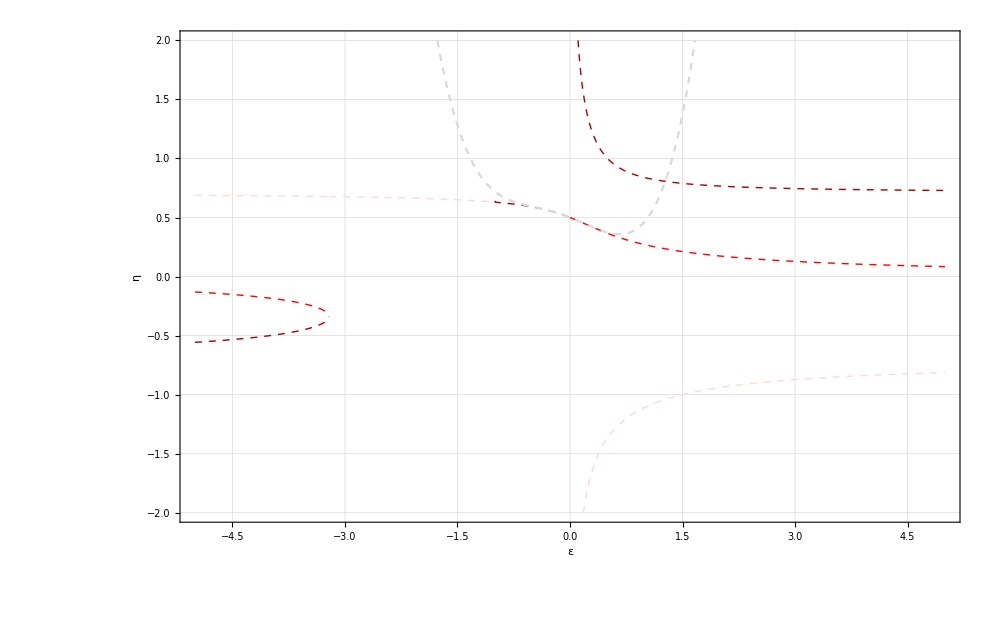

```mathematica
Plot[{eta1[ε,avir,amax,-1],eta2[ε,avir,amax,-1],eta3[ε,avir,amax,-1],eta0[ε,avir,amax,-1],eta01[ε,avir,amax,-1]},{ε,-5,5},PlotRange->{-2,2},PlotStyle->{{Darker[Red],Dashed,Thick},{LightRed,Dashed,Thick},{Red,Dashed,Thick},{LightGray,Dashed},{Gray,Dashed}},AxesLabel->{"ε","η"},LabelStyle->30,PlotTheme->"Grid",Frame->True,ImageSize->1000]
```

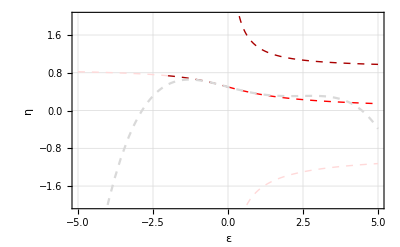

```mathematica
Plot01=Plot[{eta1[ε,0.8,0.5,-2/3],eta2[ε,0.8,0.5,-2/3],eta3[ε,0.8,0.5,-2/3],eta0[ε,0.8,0.5,-2/3],eta01[ε,0.8,0.5,-2/3]},{ε,-5,5},PlotRange->{-2,2},PlotStyle->{{Darker[Red],Dashed,Thick},{LightRed,Dashed,Thick},{Red,Dashed,Thick},{LightGray,Dashed},{Gray,Dashed}},AxesLabel->{"ε","η"},LabelStyle->20,PlotTheme->"Grid",Frame->True]
```

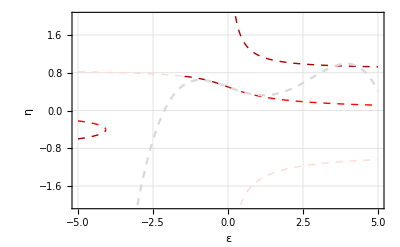

```mathematica
Plot02=Plot[{eta1[ε,0.4,0.2,-0.8],eta2[ε,0.4,0.2,-0.8],eta3[ε,0.4,0.2,-0.8],eta0[ε,0.4,0.2,-0.8],eta01[ε,0.4,0.2,-0.8]},{ε,-5,5},PlotRange->{-2,2},PlotStyle->{{Darker[Red],Dashed,Thick},{LightRed,Dashed,Thick},{Red,Dashed,Thick},{LightGray,Dashed},{Gray,Dashed}},AxesLabel->{"ε","η"},LabelStyle->20,PlotTheme->"Grid",Frame->True]
```

### Figure B1. This diagram presents three individual solutions, depicted in various shades of red, that arise from equation ( B30). For the top graph, the parameters are set to w = -2/3, a_vir = 0.8, and a_max = 0.5. Conversely, the bottom graph is characterized by w = -0.8, a_vir = 0.4 , and a_max = 0.5 for demonstration. Both plots also include a light gray line, indicative of a fourth-order approximation from equation ( B32). This highlights the accuracy of the approximation solution of (B32) when ε is significantly less than 1.

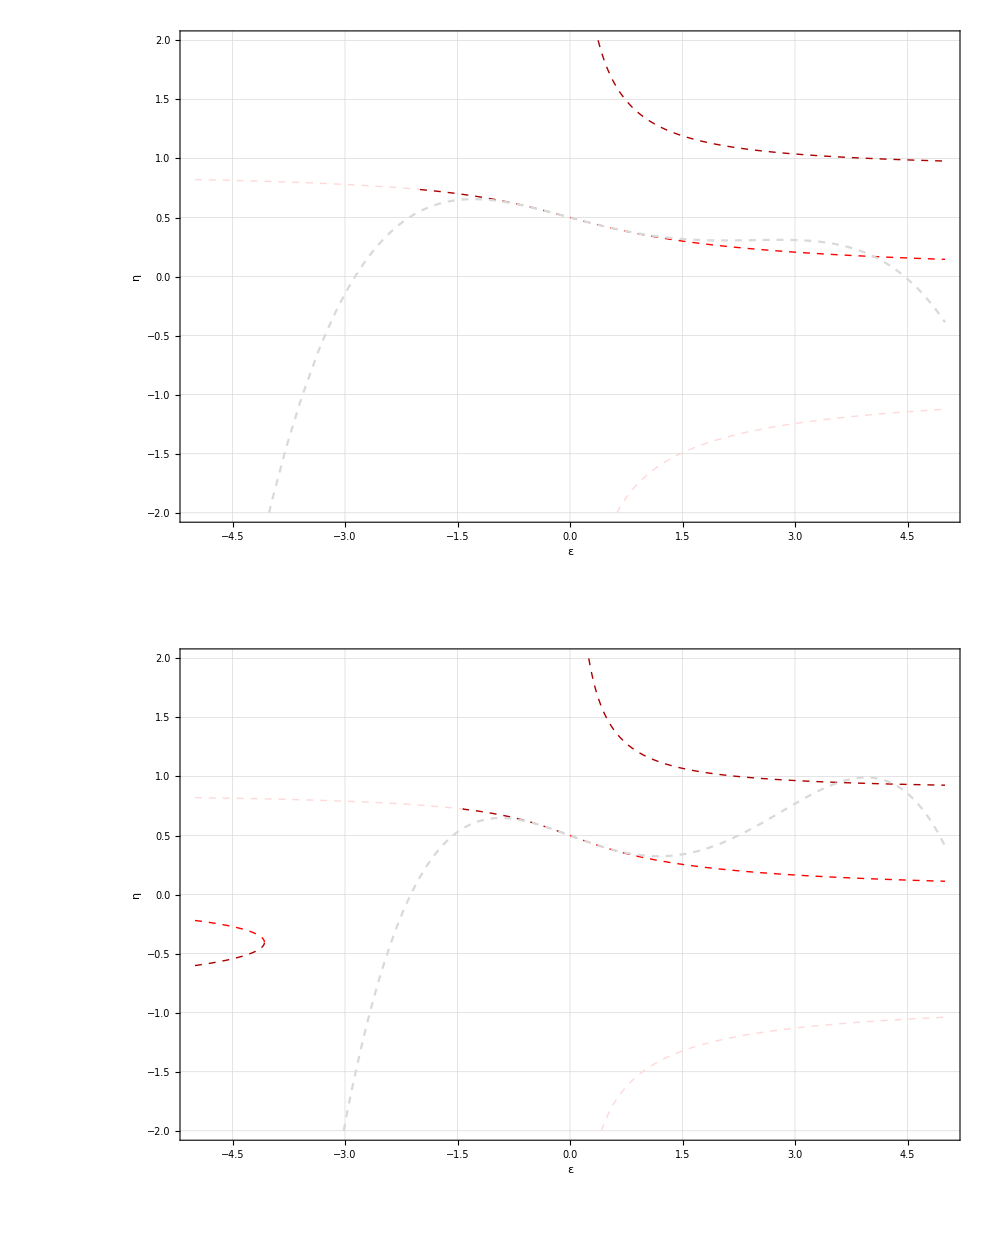

```mathematica
fsize=50;
plot1b=Show[Plot01,Frame->{{True,True},{True,True}},PlotRange->{{-5,5},{-2,2}},LabelStyle->{30,GrayLevel[0]}];
plot2b=Show[Plot02,Frame->{{True,True},{True,True}},PlotRange->{{-5,5},{-2,2}},LabelStyle->{30,GrayLevel[0]}];

figure01=GraphicsGrid[{{plot1b},{plot2b}},Spacings->0,ImageSize->1000]
```